# ChemicalData

ChemicalDataより結合情報（隣接情報）を取り出して利用する例。

デフォルトのChemicalData[]で得られるオブジェクトはGraphics:

```mathematica
ChemicalData["Caffeine"]//Head
```

Graphics

隣接行列の取得は、したがって、”AdjacencyMatrix”オプションが必要となる:

```mathematica
cd=ChemicalData["Caffeine","AdjacencyMatrix"]
```

SparseArray[…]

隣接行列をグラフにする:

```mathematica
AdjacencyGraph[cd]
```

-Graphics-

頂点に原子名を表示させるには、まず、ラベルを作成し、

```mathematica
vl=ChemicalData["Caffeine","VertexTypes"]
```

{O,O,N,N,N,N,C,C,C,C,C,C,C,C,H,H,H,H,H,H,H,H,H,H}

```mathematica
vname=Table[n->vl[[n]],{n,Length[vl]}]
```

{1→O,2→O,3→N,4→N,5→N,6→N,7→C,8→C,9→C,10→C,11→C,12→C,13→C,14→C,15→H,16→H,17→H,18→H,19→H,20→H,21→H,22→H,23→H,24→H}

オプションとして与える:

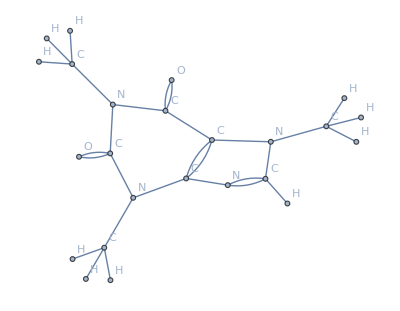

```mathematica
AdjacencyGraph[cd,VertexLabels->vname]
```

ラベルが不要ならばMoleculeGraphが使える：

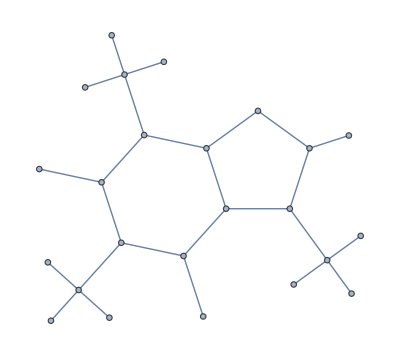

```mathematica
MoleculeGraph[Molecule["Caffeine"]]
```

ちなみに、”StructureGraph”オプションによりグラフを得ることができるが、

```mathematica
ChemicalData["Caffeine","StructureGraph"]//Head
```

Graph

GraphがAtomであるため部分構造の取り出しができない:

```mathematica
FullForm[ChemicalData["Caffeine","StructureGraph"]][[2]]
```

Part::partw: Graph[List[1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24],List[Null,SparseArray[Automatic,«2»,List[1,List[List[0,1,2,5,8,11,13,16,19,22,25,28,32,36,40,41,42,43,44,45,46,47,48,49,50],List[List[9],List[10],«46»,List[14],List[14]]],Pattern]]],List[Rule[BaseStyle,GrayLevel[0]],«3»,Rule[VertexSize,List[0.34]]]]の部分2は存在しません．

Graph[List[1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24],List[Null,SparseArray[Automatic,List[24,24],0,List[1,List[List[0,1,2,5,8,11,13,16,19,22,25,28,32,36,40,41,42,43,44,45,46,47,48,49,50],List[List[9],List[10],List[8],List[10],List[12],List[7],List[11],List[13],List[9],List[10],List[14],List[8],List[11],List[4],List[8],List[9],List[3],List[6],List[7],List[1],List[5],List[7],List[2],List[3],List[5],List[4],List[6],List[15],List[3],List[16],List[17],List[18],List[4],List[19],List[20],List[21],List[5],List[22],List[23],List[24],List[11],List[12],List[12],List[12],List[13],List[13],List[13],List[14],List[14],List[14]]],Pattern]]],List[Rule[BaseStyle,GrayLevel[0]],Rule[EdgeShapeFunction,List[Rule[UndirectedEdge[6,11],Function[GraphComputation`GraphBuilderDump`ef[Slot[1],2]]],Rule[UndirectedEdge[7,8],Function[GraphComputation`GraphBuilderDump`ef[Slot[1],2]]],Rule[UndirectedEdge[2,10],Function[GraphComputation`GraphBuilderDump`ef[Slot[1],2]]],Rule[UndirectedEdge[1,9],Function[GraphComputation`GraphBuilderDump`ef[Slot[1],2]]]]],Rule[VertexCoordinates,List[List[373.21,200.],List[200.,-100.],List[373.21,-100.],List[554.43,80.47],List[286.6,50.],List[554.43,-80.47],List[459.81,50.],List[459.81,-50.],List[373.21,100.],List[286.6,-50.],List[612.79,0.],List[373.21,-200.],List[585.5,175.53],List[200.,100.],List[674.79,0.],List[311.21,-200.],List[373.21,-262.],List[435.21,-200.],List[644.43,156.26],List[604.76,234.46],List[526.56,194.79],List[231.,153.69],List[146.31,131.],List[169.,46.31]]],Rule[VertexShape,List[Rule[13,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["C",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[10,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["C",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[9,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["C",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[23,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["H",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[20,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["H",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[3,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["N",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[19,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["H",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[4,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["N",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[24,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["H",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[18,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["H",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[14,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["C",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[6,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["N",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[22,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["H",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[2,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["O",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[17,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["H",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[8,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["C",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[21,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["H",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[15,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["H",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[5,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["N",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[11,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["C",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[16,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["H",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[12,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["C",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[7,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["C",Rule[FontSize,Scaled[1]]],List[0,0]]]]],Rule[1,Graphics[List[GrayLevel[1],Disk[List[0,0]],GrayLevel[0],Inset[Style["O",Rule[FontSize,Scaled[1]]],List[0,0]]]]]]],Rule[VertexSize,List[0.34]]]]⟦2⟧

原子の座標を得るには”AtomPositions”オプションを使用する:

```mathematica
ChemicalData["Caffeine","AtomPositions"]
```

{{24.134 pm,-147.93 pm,193.37 pm},{-287.16 pm,-54.68 pm,-121.3 pm},{-93.553 pm,62.099 pm,-135.25 pm},{203.9 pm,53.968 pm,68.284 pm},{-135.82 pm,-104.67 pm,38.896 pm},{138.96 pm,169.08 pm,-113.29 pm},{80.333 pm,14.21 pm,33.387 pm},{40.141 pm,85.578 pm,-78.341 pm},{-9.1854 pm,-85.421 pm,96.284 pm},{-177.11 pm,-32.589 pm,-74.348 pm},{239.2 pm,149.09 pm,-23.529 pm},{-139.62 pm,135.07 pm,-252.54 pm},{287.15 pm,5.3462 pm,180.66 pm},{-226.77 pm,-204.28 pm,97.556 pm},{332.92 pm,200.72 pm,-24.573 pm},{-227.73 pm,190.48 pm,-227.75 pm},{-161.9 pm,65.917 pm,-331.1 pm},{-63.072 pm,202.44 pm,-284.98 pm},{304.9 pm,-99.54 pm,169.13 pm},{236.14 pm,22.934 pm,273.06 pm},{380.59 pm,57.505 pm,181. pm},{-207.86 pm,-212.37 pm,202.57 pm},{-328.1 pm,-173.72 pm,81.802 pm},{-210.51 pm,-299.23 pm,50.977 pm}}

しかしながら、この座標はPubchemのものとはかなり異なる:
（ソースはなんであろうか？）

```mathematica
URLRead["https://pubchem.ncbi.nlm.nih.gov/rest/pug/compound/CID/2519/record/SDF/?record_type=3d&response_type=display","Body"]
```

2519
  -OEChem-09012200013D

 24 25  0     0  0  0  0  0  0999 V2000
    0.4700    2.5688    0.0006 O   0  0  0  0  0  0  0  0  0  0  0  0
   -3.1271   -0.4436   -0.0003 O   0  0  0  0  0  0  0  0  0  0  0  0
   -0.9686   -1.3125    0.0000 N   0  0  0  0  0  0  0  0  0  0  0  0
    2.2182    0.1412   -0.0003 N   0  0  0  0  0  0  0  0  0  0  0  0
   -1.3477    1.0797   -0.0001 N   0  0  0  0  0  0  0  0  0  0  0  0
    1.4119   -1.9372    0.0002 N   0  0  0  0  0  0  0  0  0  0  0  0
    0.8579    0.2592   -0.0008 C   0  0  0  0  0  0  0  0  0  0  0  0
    0.3897   -1.0264   -0.0004 C   0  0  0  0  0  0  0  0  0  0  0  0
    0.0307    1.4220   -0.0006 C   0  0  0  0  0  0  0  0  0  0  0  0
   -1.9061   -0.2495   -0.0004 C   0  0  0  0  0  0  0  0  0  0  0  0
    2.5032   -1.1998    0.0003 C   0  0  0  0  0  0  0  0  0  0  0  0
   -1.4276   -2.6960    0.0008 C   0  0  0  0  0  0  0  0  0  0  0  0
    3.1926    1.2061    0.0003 C   0  0  0  0  0  0  0  0  0  0  0  0
   -2.2969    2.1881    0.0007 C   0  0  0  0  0  0  0  0  0  0  0  0
    3.5163   -1.5787    0.0008 H   0  0  0  0  0  0  0  0  0  0  0  0
   -1.0451   -3.1973   -0.8937 H   0  0  0  0  0  0  0  0  0  0  0  0
   -2.5186   -2.7596    0.0011 H   0  0  0  0  0  0  0  0  0  0  0  0
   -1.0447   -3.1963    0.8957 H   0  0  0  0  0  0  0  0  0  0  0  0
    4.1992    0.7801    0.0002 H   0  0  0  0  0  0  0  0  0  0  0  0
    3.0468    1.8092   -0.8992 H   0  0  0  0  0  0  0  0  0  0  0  0
    3.0466    1.8083    0.9004 H   0  0  0  0  0  0  0  0  0  0  0  0
   -1.8087    3.1651   -0.0003 H   0  0  0  0  0  0  0  0  0  0  0  0
   -2.9322    2.1027    0.8881 H   0  0  0  0  0  0  0  0  0  0  0  0
   -2.9346    2.1021   -0.8849 H   0  0  0  0  0  0  0  0  0  0  0  0
  1  9  2  0  0  0  0
  2 10  2  0  0  0  0
  3  8  1  0  0  0  0
  3 10  1  0  0  0  0
  3 12  1  0  0  0  0
  4  7  1  0  0  0  0
  4 11  1  0  0  0  0
  4 13  1  0  0  0  0
  5  9  1  0  0  0  0
  5 10  1  0  0  0  0
  5 14  1  0  0  0  0
  6  8  1  0  0  0  0
  6 11  2  0  0  0  0
  7  8  2  0  0  0  0
  7  9  1  0  0  0  0
 11 15  1  0  0  0  0
 12 16  1  0  0  0  0
 12 17  1  0  0  0  0
 12 18  1  0  0  0  0
 13 19  1  0  0  0  0
 13 20  1  0  0  0  0
 13 21  1  0  0  0  0
 14 22  1  0  0  0  0
 14 23  1  0  0  0  0
 14 24  1  0  0  0  0
M  END
> <PUBCHEM_COMPOUND_CID>
2519

> <PUBCHEM_CONFORMER_RMSD>
0.4

> <PUBCHEM_CONFORMER_DIVERSEORDER>
1

> <PUBCHEM_MMFF94_PARTIAL_CHARGES>
15
1 -0.57
10 0.69
11 0.04
12 0.3
13 0.26
14 0.3
15 0.15
2 -0.57
3 -0.42
4 0.05
5 -0.42
6 -0.57
7 -0.24
8 0.29
9 0.71

> <PUBCHEM_EFFECTIVE_ROTOR_COUNT>
0

> <PUBCHEM_PHARMACOPHORE_FEATURES>
5
1 1 acceptor
1 2 acceptor
3 4 6 11 cation
5 4 6 7 8 11 rings
6 3 5 7 8 9 10 rings

> <PUBCHEM_HEAVY_ATOM_COUNT>
14

> <PUBCHEM_ATOM_DEF_STEREO_COUNT>
0

> <PUBCHEM_ATOM_UDEF_STEREO_COUNT>
0

> <PUBCHEM_BOND_DEF_STEREO_COUNT>
0

> <PUBCHEM_BOND_UDEF_STEREO_COUNT>
0

> <PUBCHEM_ISOTOPIC_ATOM_COUNT>
0

> <PUBCHEM_COMPONENT_COUNT>
1

> <PUBCHEM_CACTVS_TAUTO_COUNT>
1

> <PUBCHEM_CONFORMER_ID>
000009D700000001

> <PUBCHEM_MMFF94_ENERGY>
22.901

> <PUBCHEM_FEATURE_SELFOVERLAP>
25.487

> <PUBCHEM_SHAPE_FINGERPRINT>
10967382 1 18338799025773621285
11132069 177 18339075025094499008
12524768 44 18342463625094026902
13140716 1 17978511158789908153
16945 1 18338517550775811621
193761 8 15816500986559935910
20588541 1 18339082691204868851
21501502 16 18338796715286957384
22802520 49 18128840606503503494
2334 1 18338516344016692929
23402539 116 18270382932679789735
23552423 10 18262240993325675966
23559900 14 18199193898169584358
241688 4 18266458702623303353
2748010 2 18266180539182415717
5084963 1 17698433339235542986
528886 8 18267580380709240570
53812653 166 18198902694142226312
66348 1 18339079396917369615

> <PUBCHEM_SHAPE_MULTIPOLES>
256.45
4.01
2.83
0.58
0.71
0.08
0
-0.48
0
-0.81
0
0.01
0
0

> <PUBCHEM_SHAPE_SELFOVERLAP>
550.88

> <PUBCHEM_SHAPE_VOLUME>
143.9

> <PUBCHEM_COORDINATE_TYPE>
2
5
10

$$$$